## Resistance data

```mathematica
(*From pore resistance simulation: 'nanoporemodel.np' notebook*)
```

```mathematica
RpDatam={{0.01,3.084034501333908*^15},{0.02,4.815156334595465*^15},{0.03,6.144893660866152*^15},{0.04,7.250037665050994*^15},{0.05,8.36066276728238*^15},{0.06,9.276964344063138*^15},{0.07,1.0069993000005158*^16},{0.08,1.0941273138122078*^16},{0.09,1.1763519144451374*^16},{0.1,1.254104407958279*^16}};
```

```mathematica
ListPlot[RpDatam,Joined->False,Frame->True,FrameLabel->{"Voltage (V)","Pore resistance (Ω)"},FrameStyle->Thick,
LabelStyle->Directive[Bold,14],PlotMarkers->Automatic]
```

-Graphics-

### Conductance

```mathematica
GpDatam={#[[1]],1/#[[2]]}&/@RpDatam
```

{{0.01,3.24251×10^-16},{0.02,2.07678×10^-16},{0.03,1.62737×10^-16},{0.04,1.3793×10^-16},{0.05,1.19608×10^-16},{0.06,1.07794×10^-16},{0.07,9.93049×10^-17},{0.08,9.1397×10^-17},{0.09,8.50086×10^-17},{0.1,7.97382×10^-17}}

### I-V Curve

I = G(V)(V-V_rev)
I considered V_rev = 0
Thus,
I = G*V

```mathematica
IpDatam={#[[1]],((#[[1]])-0.005)*#[[2]]}&/@GpDatam
```

{{0.01,1.62125×10^-18},{0.02,3.11516×10^-18},{0.03,4.06842×10^-18},{0.04,4.82756×10^-18},{0.05,5.38235×10^-18},{0.06,5.92866×10^-18},{0.07,6.45482×10^-18},{0.08,6.85478×10^-18},{0.09,7.22573×10^-18},{0.1,7.57513×10^-18}}

## 2S3B Fitting

#### Our data

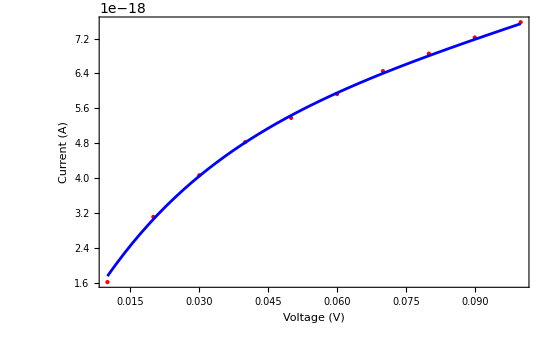

{A→2.15569,α→-0.673096,G23→-0.703457,d1→0.0281974,d2→0.0439561,d3→0.43204}

```mathematica
(*---Constants---*)
z=1;
F=96485;
R=8.314;
T=298;
scaleV=z*F/(R*T); 
Q=1*^-21;               (*Kinetic prefactor*)
γ=0.8;      (*Activity coefficient*)
Sbath=γ*140;
Spipette=γ*140;

(*---I-V Data:voltage in V,current in A---*)
cntData=IpDatam;

(*---Scale voltage only---*)
scaledData={#[[1]]*scaleV,#[[2]]}&/@cntData;

(*---2S3B Model (from the article: equqtion 9)---*)
model[vs_,A_,α_,(*G3_,*)G23_,d1_,d2_,d3_]:=z*F*Q*Exp[-G23+(*G3**)(1+α)]*A*(Exp[(d2+2*d1)*vs]/Sbath-Exp[-(d2+2*d3)*vs]/Spipette);

(*---Nonlinear Fit---**)
fit=NonlinearModelFit[scaledData,model[vs,A,α,(*G3,*)G23,d1,d2,d3],{{A,2.45},{α(*G2/G3*),-0.66},(*{G3,1},*){G23,-0.72},{d1,.03},{d2,.02},{d3,.5(*.713*)}},vs];

(*---Wrapper to input real voltage V (in Volts) and scale internally---*)
fitPhysical[V_]:=fit[V*scaleV]

(*---Plot:original data vs model evaluated on physical voltage---*)
Show[ListPlot[cntData,PlotStyle->{Red,PointSize[Medium]},Frame->True,FrameLabel->{"Voltage (V)","Current (A)"}(*,PlotLegends->{"Experimental Data"}*),FrameStyle->Thick,
LabelStyle->Directive[Bold,14]],Plot[fitPhysical[V],{V,0.01,0.1},PlotStyle->Blue],PlotRange->All(*,PlotLegends->{"Model Fit"}*)]

(*---Output best-fit parameters---*)
fit["BestFitParameters"]
```